```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
ClearAll[λ]
```

## LASER dataset for the samples A, B, C, D and perovskite

```mathematica
titles={"Sample A","Sample B","Sample C","Sample D","Perovskite"};
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/NP/esperimento/LASER/laser_``.txt",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"λ (nm)"->1,"I"->2|>]&/@{"sample_A","sample_B","sample_C","sample_D","perovskite2"};
```

```mathematica
data=Transpose[{#[All,"λ (nm)"],#[All,"I"]}//Normal]&/@data;
```

```mathematica
lamPk=FindPeaks[#,100,Automatic,0.1]&/@(TimeSeriesResample@TimeSeries[#2,{#1}]&@@@(Transpose[#]&/@data))//Normal;
```

```mathematica
Rule@@@Transpose[{titles,Column@Flatten@Take[#,All,1]&/@lamPk}]//Association//Dataset
```

```mathematica
ListLinePlot[data,PlotRange->All,AxesLabel->{"λ (nm)","I"}]//Show[#,ListPlot[lamPk,PlotLabels->titles],ImageSize->Large,PlotRange->All]&
```

-Graphics-

```mathematica
lamIntervals={{400,530},{500,650},{600,750},{450,650},{550,650}};
valsInt=Cases[#1,{x_,y_}/;#2[[1]]<=x<=#2[[2]]]&@@@Transpose[{data,lamIntervals}];
```

```mathematica
fitFn=NonlinearModelFit[#1,A ⅇ^(-(λ-μ)^2/(2 σ^2)),{A,{μ,#2},σ},λ]&@@@Transpose[{valsInt,{460.5,554.3,672.47,550.4,571.5}}];
```

General::munfl: Exp[-828.781] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2613.35] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-750.007] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

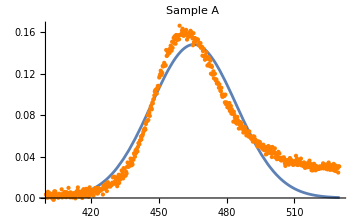
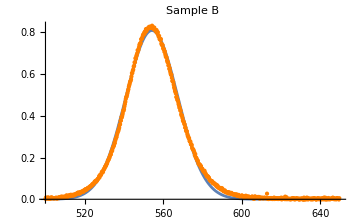
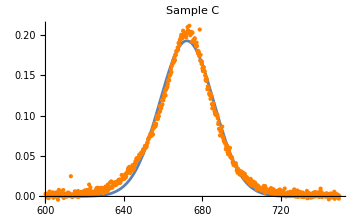
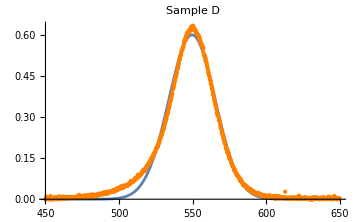
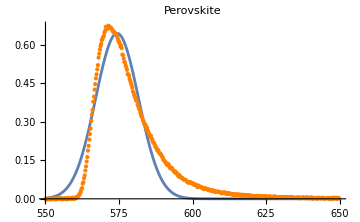
-Graphics- |  | DF | SS | MS
Model | 3 | 3.33954 | 1.11318
Error | 588 | 0.142996 | 0.00024319
Uncorrected Total | 591 | 3.48254 | 
Corrected Total | 590 | 1.47775 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.148411 | 0.00155118 | 95.6765 | 0.
μ | 465.551 | 0.226788 | 2052.8 | 0.
σ | 18.7921 | 0.226815 | 82.8519 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 68.4555 | 22.8185
Error | 664 | 0.122707 | 0.000184799
Uncorrected Total | 667 | 68.5782 | 
Corrected Total | 666 | 45.7676 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.808636 | 0.00162721 | 496.945 | 0.
μ | 554.26 | 0.0307381 | 18031.7 | 0.
σ | 13.2287 | 0.0307377 | 430.374 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 3.95992 | 1.31997
Error | 651 | 0.0298337 | 0.0000458274
Uncorrected Total | 654 | 3.98976 | 
Corrected Total | 653 | 2.54211 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.192741 | 0.000803042 | 240.013 | 0.
μ | 672.052 | 0.0663241 | 10132.9 | 0.
σ | 13.786 | 0.0663233 | 207.861 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 44.8615 | 14.9538
Error | 891 | 0.282091 | 0.0003166
Uncorrected Total | 894 | 45.1436 | 
Corrected Total | 893 | 30.961 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.600014 | 0.00195221 | 307.352 | 0.
μ | 549.599 | 0.0590979 | 9299.8 | 0.
σ | 15.7305 | 0.0590969 | 266.181 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 23.804 | 7.93468
Error | 439 | 1.16107 | 0.0026448
Uncorrected Total | 442 | 24.9651 | 
Corrected Total | 441 | 17.4937 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.643393 | 0.00830639 | 77.4576 | 3.85314×10^-258
μ | 574.345 | 0.10877 | 5280.35 | 0.
σ | 7.29657 | 0.108786 | 67.0728 | 7.79074×10^-233

```mathematica
{Show[Plot[#1[λ],{λ,#3[[1]],#3[[2]]},ImageSize->Medium,PlotLabel->#4],ListPlot[#2,PlotStyle->{Orange,PointSize[Small]}],PlotRange->All],Column[{#1["ANOVATable"],"",#1["ParameterTable"]}]}&@@@Transpose[{fitFn,valsInt,lamIntervals,titles}]//TableForm
```

## UV dataset for the samples A, B, C, D

```mathematica
titles={"Sample A","Sample B","Sample C","Sample D"};
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/NP/esperimento/uvNewCorrect/sample``.txt",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"λ (nm)"->1,"I"->2|>]&/@{"A","B","C","D"};
```

```mathematica
data=Transpose[{#[All,"λ (nm)"],#[All,"I"]}//Normal]&/@data;
```

```mathematica
lamPk=FindPeaks[#,50,Automatic,0.05]&/@(TimeSeriesResample@TimeSeries[#2,{#1}]&@@@(Transpose[#]&/@data))//Normal;
```

```mathematica
Rule@@@Transpose[{titles,Column@Flatten@Take[#,All,1]&/@lamPk}]//Association//Dataset
```

```mathematica
ListLinePlot[data,PlotRange->All,AxesLabel->{"λ (nm)","I"}]//Show[#,ListPlot[lamPk,PlotLabels->titles],ImageSize->Large,PlotRange->All]&
```

-Graphics-

```mathematica
lamIntervals={{440,500},{480,650},{600,750},{500,650}};
valsInt=Cases[#1,{x_,y_}/;#2[[1]]<=x<=#2[[2]]]&@@@Transpose[{data,lamIntervals}];
```

```mathematica
fitFn=NonlinearModelFit[#1,A ⅇ^(-(λ-μ)^2/(2 σ^2)),{A,{μ,#2},σ},λ]&@@@Transpose[{valsInt,{467.25,553.68,672.47,557.4}}]
```

{FittedModel[0.106529 ⅇ^(-0.00153351 (-«19»+λ)^2)],FittedModel[0.875347 ⅇ^(-0.00256873 (-«18»+λ)^2)],FittedModel[0.191232 ⅇ^(-0.00237737 (-«18»+λ)^2)],FittedModel[0.157592 ⅇ^(-0.00236518 (-«18»+λ)^2)]}

General::munfl: Exp[-1422.88] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2189.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4855.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

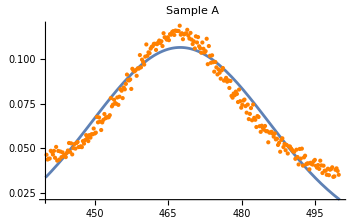
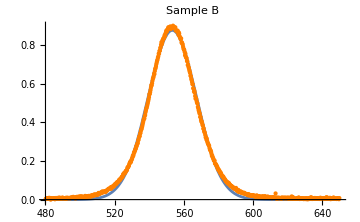
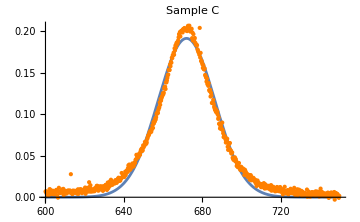
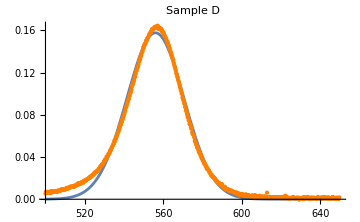
-Graphics- |  | DF | SS | MS
Model | 3 | 1.61686 | 0.538954
Error | 269 | 0.0121337 | 0.0000451066
Uncorrected Total | 272 | 1.629 | 
Corrected Total | 271 | 0.182624 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.106529 | 0.000721465 | 147.656 | 1.7627×10^-259
μ | 467.477 | 0.145401 | 3215.09 | 0.
σ | 18.0569 | 0.176268 | 102.44 | 1.5823×10^-217
-Graphics- |  | DF | SS | MS
Model | 3 | 84.6172 | 28.2057
Error | 754 | 0.171484 | 0.000227432
Uncorrected Total | 757 | 84.7887 | 
Corrected Total | 756 | 57.893 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.875347 | 0.00175761 | 498.033 | 0.
μ | 553.295 | 0.0323471 | 17104.9 | 0.
σ | 13.9517 | 0.0323466 | 431.317 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 4.10082 | 1.36694
Error | 651 | 0.039738 | 0.0000610415
Uncorrected Total | 654 | 4.14056 | 
Corrected Total | 653 | 2.48463 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.191232 | 0.000903615 | 211.63 | 0.
μ | 671.905 | 0.0791273 | 8491.44 | 0.
σ | 14.5023 | 0.0791263 | 183.28 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 2.85658 | 0.952194
Error | 664 | 0.0145978 | 0.0000219847
Uncorrected Total | 667 | 2.87118 | 
Corrected Total | 666 | 1.77811 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.157592 | 0.000535448 | 294.318 | 0.
μ | 556.035 | 0.057043 | 9747.66 | 0.
σ | 14.5396 | 0.0570424 | 254.891 | 0.

```mathematica
{Show[Plot[#1[λ],{λ,#3[[1]],#3[[2]]},ImageSize->Medium,PlotLabel->#4],ListPlot[#2,PlotStyle->{Orange,PointSize[Small]}],PlotRange->All],Column[{#1["ANOVATable"],"",#1["ParameterTable"]}]}&@@@Transpose[{fitFn,valsInt,lamIntervals,titles}]//TableForm
```

```mathematica
selVal=Cases[First@data,{x_,y_}/;300<=x<=900];
```

```mathematica
fiti=NonlinearModelFit[selVal,Subscript[A, 1] ⅇ^(-(λ-Subscript[μ, 1])^2/(2 Subscript[σ, 1]^2))+Subscript[A, 2] ⅇ^(-(λ-Subscript[μ, 2])^2/(2 Subscript[σ, 2]^2))+Subscript[A, 3] ⅇ^(-(λ-Subscript[μ, 3])^2/(2 Subscript[σ, 3]^2)),{Subscript[A, 1],{Subscript[μ, 1],406},Subscript[σ, 1],Subscript[A, 2],{Subscript[μ, 2],467.25},Subscript[σ, 2],Subscript[A, 3],{Subscript[μ, 3],600},Subscript[σ, 3]},λ];
```

General::munfl: 0.721808 2.52765×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.51] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.752] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

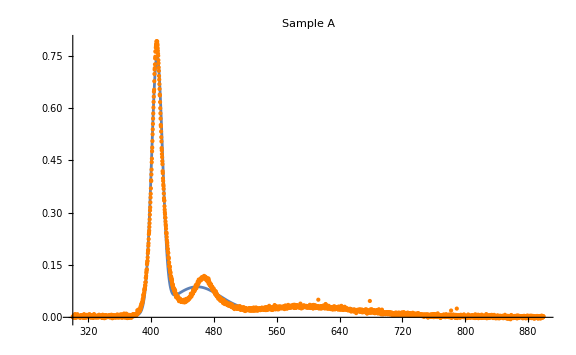
-Graphics-
 | DF | SS | MS
Model | 9 | 35.2949 | 3.92165
Error | 2655 | 0.31184 | 0.000117454
Uncorrected Total | 2664 | 35.6067 | 
Corrected Total | 2663 | 30.6546 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A_1 | 0.721808 | 0.0020422 | 353.446 | 0.
μ_1 | 407.373 | 0.0199268 | 20443.5 | 0.
σ_1 | 6.95133 | 0.0245919 | 282.668 | 0.
A_2 | 0.0842021 | 0.000954082 | 88.2545 | 0.
μ_2 | 457.219 | 0.520148 | 879.017 | 0.
σ_2 | 32.0018 | 0.635717 | 50.3396 | 0.
A_3 | 0.0301523 | 0.000588465 | 51.2389 | 0.
μ_3 | 606.328 | 2.20443 | 275.05 | 0.
σ_3 | 70.8791 | 2.38818 | 29.6792 | 2.04606×10^-167

```mathematica
{Show[Plot[fiti[λ],{λ,300,900},ImageSize->Large,PlotRange->All,PlotLabel->"Sample A"],ListPlot[selVal,PlotStyle->{Orange,PointSize[Small]}],PlotRange->All],Column[{fiti["ANOVATable"],"",fiti["ParameterTable"]}]}//TableForm
```

## Green, red and UV LEDs spectra

```mathematica
titles={"Green LED","Red LED","UV LED"};
data=Dataset[Import[ToString@StringForm["/Users/giovannigravili/Library/Mobile Documents/com~apple~CloudDocs/LM MANO/Notebooks/NP/esperimento/LEDs/``LedTxt.txt",#],"Table","HeaderLines"->0,"FieldSeparators"->"\t","NumberPoint"->".",CharacterEncoding->"UTF8"]][All,Range[1,2]][All,<|"λ (nm)"->1,"I"->2|>]&/@{"green","red","uv"};
```

```mathematica
data=Transpose[{#[All,"λ (nm)"],#[All,"I"]}//Normal]&/@data;
```

```mathematica
lamPk=FindPeaks[#,100,Automatic,0.05]&/@(TimeSeriesResample@TimeSeries[#2,{#1}]&@@@(Transpose[#]&/@data))//Normal;
```

```mathematica
Rule@@@Transpose[{titles,Column@Flatten@Take[#,All,1]&/@lamPk}]//Association//Dataset
```

```mathematica
ListLinePlot[data,PlotRange->All,AxesLabel->{"λ (nm)","I"}]//Show[#,ListPlot[lamPk,PlotLabels->titles],ImageSize->Large,PlotRange->All]&
```

-Graphics-

```mathematica
lamIntervals={{500,650},{580,800},{360,450}};
valsInt=Cases[#1,{x_,y_}/;#2[[1]]<=x<=#2[[2]]]&@@@Transpose[{data,lamIntervals}];
```

```mathematica
fitFn=NonlinearModelFit[#1,A ⅇ^(-(λ-μ)^2/(2 σ^2)),{A,{μ,#2},σ},λ]&@@@Transpose[{valsInt,{560.9,686.4,406.6}}]
```

{FittedModel[0.0623024 ⅇ^(-0.00275522 (-«18»+λ)^2)],FittedModel[0.183749 ⅇ^(-0.00299913 (-«18»+λ)^2)],FittedModel[0.10579 ⅇ^(-0.00947149 (-«18»+λ)^2)]}

General::munfl: Exp[-1155.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3532.45] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1063.13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

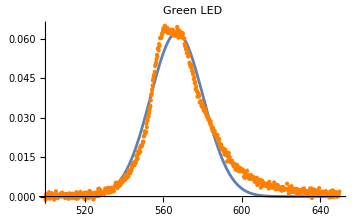
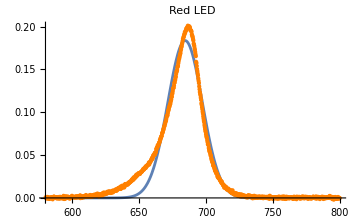
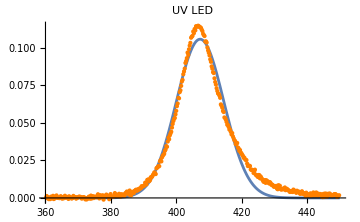
-Graphics- |  | DF | SS | MS
Model | 3 | 0.412719 | 0.137573
Error | 664 | 0.00884482 | 0.0000133205
Uncorrected Total | 667 | 0.421563 | 
Corrected Total | 666 | 0.26772 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.0623024 | 0.000433495 | 143.721 | 0.
μ | 567. | 0.108231 | 5238.78 | 0.
σ | 13.4712 | 0.10823 | 124.469 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 3.36313 | 1.12104
Error | 954 | 0.0776968 | 0.0000814432
Uncorrected Total | 957 | 3.44083 | 
Corrected Total | 956 | 2.59732 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.183749 | 0.00110745 | 165.92 | 0.
μ | 684.39 | 0.0898578 | 7616.37 | 0.
σ | 12.9118 | 0.0898569 | 143.693 | 0.
-Graphics- |  | DF | SS | MS
Model | 3 | 0.665053 | 0.221684
Error | 412 | 0.00903571 | 0.0000219313
Uncorrected Total | 415 | 0.674089 | 
Corrected Total | 414 | 0.451651 | 

 | Estimate | Standard Error | t-Statistic | P-Value
A | 0.10579 | 0.000744038 | 142.184 | 0.
μ | 407.296 | 0.0590058 | 6902.65 | 0.
σ | 7.26567 | 0.0590055 | 123.136 | 0.

```mathematica
{Show[Plot[#1[λ],{λ,#3[[1]],#3[[2]]},ImageSize->Medium,PlotLabel->#4],ListPlot[#2,PlotStyle->{Orange,PointSize[Small]}],PlotRange->All],Column[{#1["ANOVATable"],"",#1["ParameterTable"]}]}&@@@Transpose[{fitFn,valsInt,lamIntervals,titles}]//TableForm
```

## Calculation of the concentration

```mathematica
λ=UnitConvert[672.84 Quantity[, "Nanometers"],"SIBase"]
```

6.7284×10^-7 m

```mathematica
c=Quantity[, "SpeedOfLight"]//UnitConvert[#,"SIBase"]&//N
```

2.99792×10^8 m/s

```mathematica
ν=UnitConvert[c/λ,"SIBase"]
```

4.45563×10^14 per second

```mathematica
m0=UnitConvert[Entity["Particle","Electron"][EntityProperty["Particle","Mass"]],"SIBase"]
```

9.109383632×10^-31 kg

```mathematica
meCdS=0.21m0
```

1.91297×10^-31 kg

```mathematica
meCdSe=0.13 m0
```

1.18422×10^-31 kg

```mathematica
mhCdS=0.64m0
mhCdSe=0.45 m0
```

5.83001×10^-31 kg

4.09922×10^-31 kg

```mathematica
h=UnitConvert[Quantity[, "PlanckConstant"],"SIBase"]//N
```

6.62607×10^-34 kg m^2/s

```mathematica
e=UnitConvert[Entity["Particle","Electron"][EntityProperty["Particle","Charge"]],"SIBase"]//N
```

-1.60218×10^-19 s A

```mathematica
r=UnitConvert[3 Quantity[, "Nanometers"],"SIBase"]//N
```

3.×10^-9 m

```mathematica
egCdS=UnitConvert[2.45 Quantity[, "Electronvolts"],"SIBase"]
```

3.92533×10^-19 kg m^2/s^2

```mathematica
egCdSe=UnitConvert[1.74 Quantity[, "Electronvolts"],"SIBase"]
```

2.78779×10^-19 kg m^2/s^2

```mathematica
b=UnitConvert[0.24 Quantity[, "Electronvolts"],"SIBase"]
```

3.84522×10^-20 kg m^2/s^2

```mathematica
eq=h ν==(x egCdS+(1-x)egCdSe-b x(1-x))+h^2/(8 r^2)(1/(x meCdS+(1-x)meCdSe)+1/(x mhCdS+(1-x)mhCdSe))
```

2.95233×10^-19 kg m^2/s^2==(1-x) x (-3.84522×10^-20 kg m^2/s^2)+(6.09789×10^-51 kg^2 m^2/s^2) (1/((1-x) (1.18422×10^-31 kg)+x (1.91297×10^-31 kg))+1/((1-x) (4.09922×10^-31 kg)+x (5.83001×10^-31 kg)))+(1-x) (2.78779×10^-19 kg m^2/s^2)+x (3.92533×10^-19 kg m^2/s^2)

```mathematica
eqn=eq/. Quantity[a_,b_]:>QuantityMagnitude[Quantity[a,b]]//Simplify;
```

```mathematica
NSolve[eq,x,Reals,WorkingPrecision->10]
```

{{x→-3.04579384},{x→-2.148838181}}

## Calculations debugging

```mathematica
h ν
```

2.95233×10^-19 kg m^2/s^2

```mathematica
(x egCdS+(1-x)egCdSe-b x(1-x))/.{x->0.9}
```

3.77697×10^-19 kg m^2/s^2

```mathematica
h^2/(8 e r^2)
```

-3.806×10^-32 kg^2 m^2/(s^3 A)

```mathematica
(1/(x meCdS+(1-x)meCdSe)+1/(x mhCdS+(1-x)mhCdSe))/.{x->0.9} (* 0.9 is just a test value *)
```

6.86949×10^30 /kg

```mathematica
h^2/(8 e r^2)(1/(x meCdS+(1-x)meCdSe)+1/(x mhCdS+(1-x)mhCdSe))/.{x->0.9}//ScientificForm
```

-2.61453×10^-1 kg m^2/(s^3 A)